# Wolfram/Arrays

Domain-neutral array container utilities over explicit, lazy, and symbolic array tiers

## Paclet Manifest

## Web Content

### Headline Image

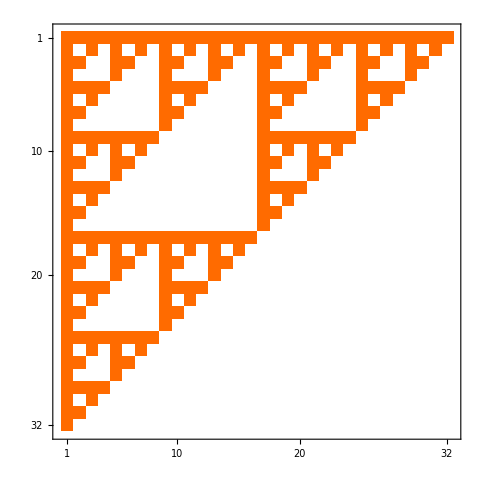

```mathematica
MatrixPlot[SparseArray[Nest[KroneckerProduct[{{1, 1}, {1, 0}}, #] &, {{1, 1}, {1, 0}}, 4]], ImageSize -> 480]
```

### Basic Description

The Arrays paclet is a domain-neutral abstraction over the array containers of the Wolfram Language: one dispatch layer for classifying, introspecting and operating on an array regardless of how it is stored. An expression is admitted as a container when its shape is introspectable without materializing its elements and a materialization path exists. Containers fall into three tiers. Explicit containers hold their elements in memory: SparseArray, packed and plain List arrays, NumericArray, structured arrays such as SymmetrizedArray, and the shape-introspectable wrappers QuantityArray, TabularColumn, Tabular, Dataset, ByteArray, EventSeries and DataStructure array stores. Lazy parametric containers are array-valued inert applications awaiting their parameters, admitted through a registry of heads: an array-valued InterpolatingFunction, a ParametricFunction, an unapplied Function, an array-valued Piecewise. Symbolic containers have no elements at all: VectorSymbol, MatrixSymbol and ArraySymbol, symbols registered in $Assumptions, and inactive tensor trees over them. Whether a container also computes in place, without materializing, is a per-head capability rather than a requirement for admission.

### Details

Every container of every tier answers ArrayDimensions and ArrayRank without materializing, and has an ArrayMaterialize route.

ArrayContainerQ is the top-level admission predicate, equivalent to ArrayExplicitQ[a] || ArrayLazyQ[a] || ArraySymbolicQ[a].

ArrayComputeNativeQ is the capability flag, not an admission gate. SparseArray, packed and plain lists, QuantityArray and TabularColumn are compute-native; NumericArray, structured arrays and the remaining wrapper containers are storage-only, as are all lazy and symbolic containers.

A storage-only container is materialized before compute and re-wrapped in its own head where a reconstruction path exists.

Structural operations keep a lazy container lazy, and slice a symbolic container structurally: ArrayPart of a MatrixSymbol is a named VectorSymbol.

ArrayReplaceAll substitutes into a lazy container as a whole, evaluating it a single time, where ArrayMaterialize expands it into one inert application per element.

ArrayObject is a handle around any supported container, formatted as a summary box. Every function takes a handle wherever it takes a container, and gives back a raw container rather than another handle.

Association is not admitted: its Dimensions and Normal report the entry multiset rather than the represented vector, so it has neither a faithful shape nor a faithful materialization.

### Primary Context

Wolfram`Arrays`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["Wolfram`Arrays`"];
```

### Basic Examples

A sparse matrix is an explicit-tier container:

```mathematica
ArrayExplicitQ[SparseArray[{{0, 1}, {2, 0}}]]
```

True

Its shape comes from the stored dimensions, not from the elements:

```mathematica
ArrayDimensions[SparseArray[{{0, 1}, {2, 0}}]]
```

{2,2}

A unit-carrying wrapper is an explicit container as well:

```mathematica
ArrayExplicitQ[QuantityArray[{{1., 2.}, {3., 4.}}, "Meters"]]
```

True

Its shape is read from the wrapper, without unwrapping the units:

```mathematica
ArrayDimensions[QuantityArray[{{1., 2.}, {3., 4.}}, "Meters"]]
```

{2,2}

A NumericArray is admitted on the same shape criterion, but is storage-only rather than compute-native:

```mathematica
ArrayComputeNativeQ[NumericArray[{1., 2.}]]
```

False

An array symbol carries a name and declared dimensions and no elements:

```mathematica
ArraySymbol["T", {2, 3, 4}]
```

T3234

It belongs to the symbolic tier:

```mathematica
ArraySymbolicQ[ArraySymbol["T", {2, 3, 4}]]
```

True

Shape flows structurally through an unevaluated Transpose:

```mathematica
ArrayDimensions[Transpose[MatrixSymbol["M", {2, 3}]]]
```

{3,2}

Solving a differential equation for a vector-valued function gives an array-valued InterpolatingFunction:

```mathematica
sol = NDSolveValue[{f'[t] == {{0, 1}, {-1, 0}} . f[t], f[0] == {1., 0.}}, f, {t, 0, 10}]
```

InterpolatingFunction[…]

Applied to a symbolic time it stays unevaluated, awaiting its parameter:

```mathematica
state = sol[tau]
```

InterpolatingFunction[…][tau]

That expression is a lazy-tier container:

```mathematica
ArrayLazyQ[state]
```

True

Its shape comes from the output dimensions of the interpolating function, with nothing evaluated:

```mathematica
ArrayDimensions[state]
```

{2}

Supplying the parameter substitutes into the container as a whole, evaluating the interpolation a single time:

```mathematica
ArrayReplaceAll[state, tau -> 0.5]
```

{0.877582,-0.479425}

A handle around a container is formatted as a summary box showing its kind and dimensions:

```mathematica
ArrayObject[NumericArray[{{1., 0.}, {0., 2.}}]]
```

ArrayObject[…]

The box of a lazy container is drawn without evaluating the interpolation:

```mathematica
ArrayObject[state]
```

ArrayObject[…]

## Source & Additional Information

### Creator

Nikolay Murzin

### Source Control Repository

https://github.com/sw1sh/Arrays

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

array container

sparse array

packed array

numeric array

symbolic array

lazy array

tensor

shape introspection

materialization

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

Link to other related material

### Compatibility

#### Wolfram Language Version

14.1+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

This paclet was developed with the assistance of Claude (Anthropic). The kernel sources, the test suite, and the literate-markdown documentation sources under docs from which the reference pages, the guide, the tech note and this definition notebook are built are model-generated; they were supervised, reviewed and hand-edited by Nikolay Murzin, who is responsible for the result.